```mathematica
eqn1=pep^2-me^2==(me+pnu-pnup)^2
eqn2=pnup Sin[thetanu]+pep Sin[thetae]==0
eqn3=pnup Cos[thetanu] +pep Cos[thetae]==pnu
```

-me^2+pep^2==(me+pnu-pnup)^2

pep Sin[thetae]+pnup Sin[thetanu]==0

pep Cos[thetae]+pnup Cos[thetanu]==pnu

```mathematica
sol=Solve[{eqn1,eqn2,eqn3},{pnup,pep,thetae}]
```

{{pnup→(-pnu^2+2 me^2 Cos[thetanu]^2+2 me pnu Cos[thetanu]^2+pnu^2 1^2+2 me^2 Sin[thetanu]^2+2 me pnu Sin[thetanu]^2+pnu^2 Sin[thetanu]^2)/(2 (-pnu Cos[thetanu]+me Cos[thetanu]^2+pnu Cos[thetanu]^2+me Sin[thetanu]^2+pnu Sin[thetanu]^2)),pep→1,thetae→ConditionalExpression[ArcTan[1,1]+1,1]},1}
 |  |  |  |

```mathematica
pnup/.sol[[1]]//FullSimplify
pnup/.sol[[2]]//FullSimplify
```

(me (me+pnu))/(me+pnu-pnu Cos[thetanu])

(me (me+pnu))/(me+pnu-pnu Cos[thetanu])

```mathematica
(-pnu^2+2 me^2 Cos[thetanu]^2+2 me pnu Cos[thetanu]^2+pnu^2 Cos[thetanu]^2+2 me^2 Sin[thetanu]^2+2 me pnu Sin[thetanu]^2+pnu^2 Sin[thetanu]^2)/(2 (-pnu Cos[thetanu]+me Cos[thetanu]^2+pnu Cos[thetanu]^2+me Sin[thetanu]^2+pnu Sin[thetanu]^2))//FullSimplify
```

(me (me+pnu))/(me+pnu-pnu Cos[thetanu])

```mathematica
D[c/(1-c),c]
```

1/(1-c)+c/(1-c)^2

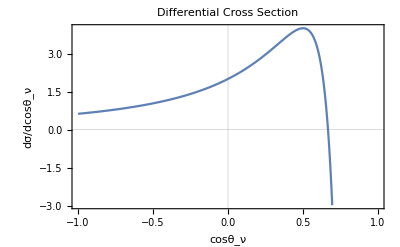

```mathematica
Plot[(1-x)^(-2)(1+(1-2x)/(1-x)),{x,-1,1},Frame->True,Axes->False,GridLines->{{0}, {0}},PlotLabel->"Differential Cross Section",FrameLabel->{"cosθ_ν","dσ/dcosθ_ν"}]
```